# Schwarzschild-Expansion of the (modified) GUP

Kempf- und Regularisierungsapproach

```mathematica
(* Vorbereitungen fuer den Export *)
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
(* Epic Epilog-Labels coming here, modified for the current problem:
   Featuring scaling and correct Inset (no rectangle nonrotated box).
 ASSUMING data be a list of X as variable, ideal for g00s. *)
ClearAll[EpiLabels]
EpiLabels[xpoint_, data_, labels_,axisratio_:1, bgcolor_:White]:= 
With[{xpoints=If[Head@xpoint===List, xpoint, xpoint&/@ labels]}, (* erlaube Liste von xpoints *)
Inset[Rotate[Text[labels[[#]],Background -> bgcolor],
ArcTan@Re@N[(D[data⟦#⟧,X]/.{X-> xpoints⟦#⟧}) ] / axisratio] ,
{xpoints⟦#⟧, 0 +( data/.X-> xpoints⟦#⟧)⟦#⟧}
]& /@ Range@Length@data] (* 1: any value to introspect list*)
```

## Worum gehts? Taylor von GUP-Term

Wir wollen die folgende Funktion g(p) taylorn. In der Regel ist also x→p und m→(N-1).

```mathematica
g[x_] = 1/(1+(L x)^m)
```

1/(1+(L x)^m)

Zeichnung dieses Prinzips:

```mathematica
(* Umstaendlicher Weg, um Mathematica zur Taylorserie zu bewegen *)
taylorg[y_,max_] := (Series[g[x]/.{m-> 1},{x,0,max}]  // Normal) /. {x-> y^m ,L-> L^m}
(* Example: *) taylorg[PONY,3]
```

1-L^m PONY^m+L^(2 m) PONY^(2 m)-L^(3 m) PONY^(3 m)

{1/(1+p^2),1,1-p^2,1-p^2+p^4,1-p^2+p^4-p^6,1-p^2+p^4-p^6+p^8}

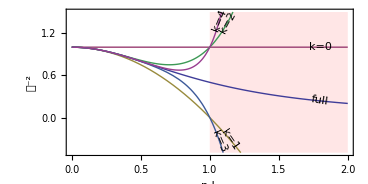

```mathematica
maxOrder = 4;
demofunks[p_] = {g[p]}~Join~Table[taylorg[p,n],{n,0,maxOrder}]/. {L-> 1, m-> 2}
demolabels = Join[{"full"},"k="<>ToString@#&/@Range[0,maxOrder]];
nonconvergenceColor=Lighter[Red,0.9];
fig=Plot[
Evaluate@demofunks[p],{p,0,2},
PlotRange-> {-0.5,1.5},
PlotRangePadding-> None,
Frame-> True,
FrameLabel-> {"p L","𝒜^-2"},
Epilog -> {
EpiLabels[{1.8,1.8,1.15,1.13,1.07,1.07}, demofunks[X],
demolabels,1.2,nonconvergenceColor]
},
Prolog-> {
nonconvergenceColor,
Rectangle[{1,-0.5},{2,1.5}]
},
AspectRatio-> 1/2,
ImageSize-> 13cm
]
```

```mathematica
Export["../figures/conv-radius.pdf", fig]
```

../figures/conv-radius.pdf

## Kempf-Ansatz

```mathematica
delta[x_] = 1/Sqrt[2π σ^2] Exp[ - x^2 / (2 σ^2) ]
```

(ⅇ^(-x^2/(2 σ^2)))/(√(2 π) √(σ^2))

```mathematica
Assuming[σ∈Reals, Integrate[delta[x],{x,-∞,∞}]]
```

1

### Dichte mit g-Approximation

```mathematica
maxOrder = 10;
(* Das sind einfache Ableitungen, geht rasend schnell *)
ClearAll[T00sOrders, T00s]
T00sOrders[m_]:= T00sOrders[m]= Table[Assuming[σ >0, 
(*SeriesCoefficient[1/(1+x),{x,0,k}] **)D[delta[x],{x,m k}]],{k,0,maxOrder}];
T00s[m_] := T00s[m]=Table[Sum[T00sOrders[m]⟦o⟧,{o,1,maxo}],{maxo, 1,maxOrder+1}]
```

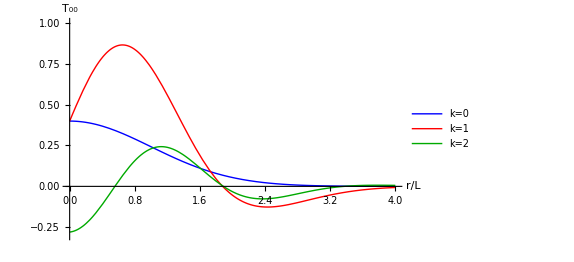

```mathematica
fig=Plot[Evaluate[{1,1,0.05} T00s[3][[1;;3]]/. {σ-> 1, x-> X}],{X,0,4},
PlotRange-> {-0.3,1},
PlotLegends->Placed[Table["k="<>ToString[n],{n,0,maxOrder}],{Right,Top}],
PlotRangePadding-> None,
PlotStyle-> {Blue,Red, Darker@Green},
AxesLabel-> {"r/L", "T_00"},
ImageSize-> 15cm
](*~Manipulate~{{S,1},0.003,3}*)
```

```mathematica
Export["../figures/t00-kempf.pdf", fig]
```

../figures/t00-kempf.pdf

```mathematica
T00s[0]
```

{(ⅇ^(-x^2/(2 σ^2)))/(√(2 π) √(σ^2)),(ⅇ^(-x^2/(2 σ^2)) √(2/π))/(√(σ^2)),(3 ⅇ^(-x^2/(2 σ^2)))/(√(2 π) √(σ^2)),(2 ⅇ^(-x^2/(2 σ^2)) √(2/π))/(√(σ^2)),(5 ⅇ^(-x^2/(2 σ^2)))/(√(2 π) √(σ^2)),(3 ⅇ^(-x^2/(2 σ^2)) √(2/π))/(√(σ^2)),(7 ⅇ^(-x^2/(2 σ^2)))/(√(2 π) √(σ^2)),(4 ⅇ^(-x^2/(2 σ^2)) √(2/π))/(√(σ^2)),(9 ⅇ^(-x^2/(2 σ^2)))/(√(2 π) √(σ^2)),(5 ⅇ^(-x^2/(2 σ^2)) √(2/π))/(√(σ^2)),(11 ⅇ^(-x^2/(2 σ^2)))/(√(2 π) √(σ^2))}

```mathematica
MsOrders[m_]:=Monitor[Table[Integrate[ T00sOrders[m]⟦o⟧ x^m,{x,0,X}],{o,1, Length@T00sOrders[m]}], o]
Ms[m_] := Ms[m]=Module[{MO= MsOrders[m]},Table[Sum[MO⟦o⟧,{o,1,maxo}],{maxo, 1,maxOrder+1}]]
```

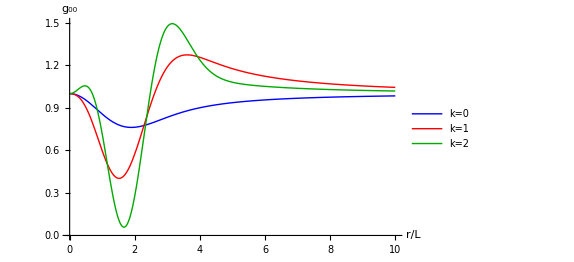

```mathematica
fig=With[{m=3},Plot[Evaluate[1-(2 {1,1,0.2}Ms[m]⟦1;;3⟧)/X^(m-1)/. σ-> 1],{X,0,10},
PlotRange-> {0,1.5},
PlotLegends->Placed[Table["k="<>ToString[n],{n,0,maxOrder}],{Right,Bottom}],
PlotRangePadding-> None,
PlotStyle-> {Blue,Red, Darker@Green},
AxesLabel-> {"r/L", "g_00"},
ImageSize-> 15cm]]
```

```mathematica
Export["../figures/g00-kempf.pdf", fig]
```

../figures/g00-kempf.pdf

## Regularisierung ∞→L statt Kempf

Möglicherweise am “Straight forwardsten” da der Konvergenzradius der Taylorreihe nur begrenzt ist: Einfach nur bis L integrieren.

Das Vorgehen ist einfach: Wir taylorn 1/(1+x) bis zu einer gewissen Ordnung und rechnen dann “brute force” die regularisierten Integrale aus. Statt L verwende ich als Limit a, wie im Latex-Dokument erwähnt.

Um eine bessere Performance beim Integrieren zu erreichen (das dauert sonst einige Minuten), rechne ich jede Ordnung nur einmal aus und addiere am Ende, statt zu beginn. Ich nehme also zu Beginn jede Ordnung für sich und rechne sie aus.

```mathematica
(* this would make the full series: *)
taylor[order_]:=(Series[1/(1+x),{x,0,order}]//Normal)/. x-> q^(N-1)
(* e.g. *)
taylor[3]
```

1-q^(-1+N)+q^(-2+2 N)-q^(-3+3 N)

```mathematica
(* This extracts one of the series order *)
tlist[order_] := (List@@taylor[order+1])⟦order+1⟧
tlist[0]
tlist[1]
tlist[2]
tlist[3]
```

1

-q^(-1+N)

q^(-2+2 N)

-q^(-3+3 N)

```mathematica
(* Expressions are now in terms of the chosen order "o". *)
(* Achtung overall (-1): Fourierrichtung exp[+Iqz] macht minus.  *)
vPlus[o_] :=- I/z q^(N-2) tlist[o];
vMinus[o_] := -(-1)^(N-1)I/z q^(N-2) (tlist[o]/. q-> (-q));
v[o_] := vPlus[o]HeavisideTheta[q] + vMinus[o]HeavisideTheta[-q];
```

```mathematica
T00[z_,o_]:= Assuming[a> 0 ∧ N ≥ 3,Integrate[v[o] Exp[I z q],{q,-a,a}]]
```

### Was können wir von der Rechnung erwarten?

Wir approximieren das Delta. Das geht eben nur im Konvergenzradius des \C A^{-2}.
Um die Effekte der “Box-Regularisierung” zu verstehen, können wir uns anschauen, wie diese Delta-Approximation (0. Ordnung) aussieht:

```mathematica
v[0]
```

(ⅈ (-1)^(-1+N) q^(-2+N) HeavisideTheta[-q])/z+(ⅈ q^(-2+N) HeavisideTheta[q])/z

```mathematica
(* Example: Zero Order *)
test = T00[z,0]
```

(-ⅈ z)^-N (-Gamma[-1+N]+Gamma[-1+N,-ⅈ a z])+(-1)^(2 N) (ⅈ z)^-N (-Gamma[-1+N]+Gamma[-1+N,ⅈ a z])

```mathematica
test//.{N-> 3} // FullSimplify
```

(ⅈ (-Gamma[2,-ⅈ a z]+Gamma[2,ⅈ a z]))/z^3

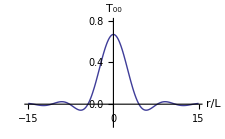

```mathematica
fig=Plot[Evaluate[test//.{N-> 3,z-> r,a-> 1.0}],{r,-15,15},
PlotRange-> {-0.2,0.8},
AxesLabel-> {"r/L", "T_00"},
ImageSize-> 8cm,
PlotRangePadding->None
]
```

```mathematica
Export["../figures/delta-box.pdf", fig]
```

../figures/delta-box.pdf

### T_00 Energiedichte ausrechnen

```mathematica
(* Die T00-Integrale ausrechnen dauert eine Weile... *)
maxOrder = 6;
T00sOrders = Monitor[Table[T00[z,order],{order,0,maxOrder}],order]
```

6

{(-ⅈ z)^-N (-Gamma[-1+N]+Gamma[-1+N,-ⅈ a z])+(-1)^(2 N) (ⅈ z)^-N (-Gamma[-1+N]+Gamma[-1+N,ⅈ a z]),(-ⅈ z)^(1-2 N) (Gamma[-2+2 N]-Gamma[-2+2 N,-ⅈ a z])+(-1)^(2 N) (ⅈ z)^(1-2 N) (Gamma[-2+2 N]-Gamma[-2+2 N,ⅈ a z]),z^2 ((-ⅈ z)^(-3 N) (Gamma[-3+3 N]-Gamma[-3+3 N,-ⅈ a z])+(-1)^(2 N) (ⅈ z)^(-3 N) (Gamma[-3+3 N]-Gamma[-3+3 N,ⅈ a z])),ⅈ z^3 ((-ⅈ z)^(-4 N) (Gamma[-4+4 N]-Gamma[-4+4 N,-ⅈ a z])+(-1)^(2 N) (ⅈ z)^(-4 N) (-Gamma[-4+4 N]+Gamma[-4+4 N,ⅈ a z])),z^4 ((-ⅈ z)^(-5 N) (-Gamma[-5+5 N]+Gamma[-5+5 N,-ⅈ a z])+(-1)^(2 N) (ⅈ z)^(-5 N) (-Gamma[-5+5 N]+Gamma[-5+5 N,ⅈ a z])),(-ⅈ z)^(1-6 N) z^4 (Gamma[-6+6 N]-Gamma[-6+6 N,-ⅈ a z])+(-1)^(2 N) (ⅈ z)^(1-6 N) z^4 (Gamma[-6+6 N]-Gamma[-6+6 N,ⅈ a z]),z^6 ((-ⅈ z)^(-7 N) (Gamma[-7+7 N]-Gamma[-7+7 N,-ⅈ a z])+(-1)^(2 N) (ⅈ z)^(-7 N) (Gamma[-7+7 N]-Gamma[-7+7 N,ⅈ a z]))}

```mathematica
(* Das hingegen geht schnell :D *)
T00s =Table[Sum[T00sOrders⟦o⟧,{o,1,maxo}],{maxo, 1,Length@T00sOrders}];
```

Check that all is real valued (it is!!), for any order and n.

```mathematica
Manipulate[
Function[Strip,Plot[Evaluate[Strip[T00s⟦order⟧] /. {z-> z,a-> l,N-> n}] ,{z,0,10}]] /@{Re,Im},
{{l,1},0,10},{n,3,7,1}, {order,1, Length@T00s,1}]
```

Part::partd: Part specification T00s ⟦ 1 ⟧ is longer than depth of object.

Make some more interesting plots

```mathematica
Manipulate[
Plot[ Evaluate@Join[{Exp[-z]/(4π z)},
Re@T00s⟦1;;4⟧ /. {z-> z,a-> l, N-> n}
],{z,0,20},
PlotLegends->Placed[Join[
{"full"},
Table[ToString[n]<>". Order",{n,1,Length@T00s}]],{Right,Top}
]
],{{l,1},0,2},{n,3,7,1}]
```

Part::take: Cannot take positions 1 through 4 in T00s.

Join::heads: Heads List and Re at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

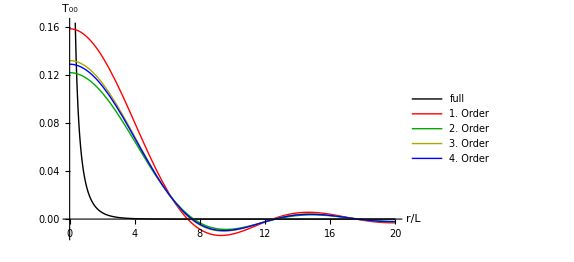

```mathematica
fig=Plot[ Evaluate@Join[{Exp[-z]/(4π z)},
Re@T00s⟦1;;4⟧ /. {z-> z,a-> 0.62, N-> 3}
],{z,0,20},
PlotLegends->Placed[Join[
{"full"},
Table[ToString[n]<>". Order",{n,1,Length@T00s}]],{Right,Top}
],
PlotRangePadding-> None,
PlotStyle-> {{Thick,Black},Red,Darker@Green,Darker@Yellow, Blue},
AxesLabel-> {"r/L", "T_00"},
ImageSize-> 15cm
]
```

```mathematica
Export["../figures/t00-regularized.pdf", fig]
```

../figures/t00-regularized.pdf

Hier mach ich Schluss und bring die Metrik-Sachen gar nicht mehr mit rein in das Latex-Dokument. Das hat allerdings eher einen technischen Grund: Die Metriken beinhalten üble Terme, die lange auszuwerten brauchen und eine numerische Integration mit variabler oberer Grenze ist auch keine besonders gute Idee.

### Massen bzw. Metrik ausrechnen

#### Exaktes Lösen der Metrik

```mathematica
(* Die Massenintegrale ausrechnen dauert auch wieder eine Weile... *)
MsOrders = Monitor[Table[
Assuming[N>3,Integrate[T00sOrders⟦order⟧ z^(N-1),{z,0,Z}]],{order,1, Length@T00s}],order]
```

{Z^N (Z^2)^-N ((-1)^(2 N) (-ⅈ Z)^N Gamma[-1+N] Log[-ⅈ a Z]-(ⅈ Z)^N Gamma[-1+N,-ⅈ a Z] Log[-ⅈ a Z]-(-1)^(2 N) (-ⅈ Z)^N Gamma[-1+N,ⅈ a Z] Log[-ⅈ a Z]+(ⅈ Z)^N Gamma[-1+N] Log[ⅈ a Z]-(ⅈ Z)^N Gamma[-1+N,-ⅈ a Z] Log[ⅈ a Z]-(-1)^(2 N) (-ⅈ Z)^N Gamma[-1+N,ⅈ a Z] Log[ⅈ a Z]-(-1)^(2 N) (-ⅈ Z)^N Gamma[-1+N] Log[a^2 Z^2]-(ⅈ Z)^N Gamma[-1+N] Log[a^2 Z^2]+(ⅈ Z)^N Gamma[-1+N,-ⅈ a Z] Log[a^2 Z^2]+(-1)^(2 N) (-ⅈ Z)^N Gamma[-1+N,ⅈ a Z] Log[a^2 Z^2]-(ⅈ Z)^N MeijerG[{{},{1,1}},{{0,0,-1+N},{}},-ⅈ a Z]-(-1)^(2 N) (-ⅈ Z)^N MeijerG[{{},{1,1}},{{0,0,-1+N},{}},ⅈ a Z]+((-1)^(2 N) (-ⅈ Z)^N+(ⅈ Z)^N) Gamma[-1+N] PolyGamma[0,-1+N]),1/(-1+N)Z^N (-(-1)^(2 N) (ⅈ Z)^(1-2 N) Gamma[-2+2 N]+ⅈ (-ⅈ Z)^(-2 N) Z Gamma[-2+2 N]+1/a(-ⅈ Z)^(-2 N) ((-ⅈ a Z)^N Gamma[-1+N]-(-ⅈ a Z)^N Gamma[-1+N,-ⅈ a Z]-ⅈ a Z Gamma[-2+2 N,-ⅈ a Z])+1/a(-1)^(2 N) (ⅈ Z)^(-2 N) ((ⅈ a Z)^N Gamma[-1+N]-(ⅈ a Z)^N Gamma[-1+N,ⅈ a Z]+ⅈ a Z Gamma[-2+2 N,ⅈ a Z])),1/2 Z^N (((-ⅈ Z)^(-3 N) Z^2 Gamma[-3+3 N])/(1-N)-((-1)^(2 N) (ⅈ Z)^(-3 N) Z^2 Gamma[-3+3 N])/(-1+N)+1/(a^2 (-1+N))(-ⅈ Z)^(-3 N) (-(-ⅈ a Z)^(2 N) Gamma[-1+N]+(-ⅈ a Z)^(2 N) Gamma[-1+N,-ⅈ a Z]+a^2 Z^2 Gamma[-3+3 N,-ⅈ a Z])+1/(a^2 (-1+N))(-1)^(2 N) (ⅈ Z)^(-3 N) (-(ⅈ a Z)^(2 N) Gamma[-1+N]+(ⅈ a Z)^(2 N) Gamma[-1+N,ⅈ a Z]+a^2 Z^2 Gamma[-3+3 N,ⅈ a Z])),1/(3 a^3 (-1+N))Z^N (Z^2)^(-4 N) (((ⅈ Z)^(4 N) (-ⅈ a Z)^(3 N)+(-1)^(2 N) (-ⅈ Z)^(4 N) (ⅈ a Z)^(3 N)) Gamma[-1+N]+ⅈ (a^3 ((-1)^(2 N) (-ⅈ Z)^(4 N)-(ⅈ Z)^(4 N)) Z^3 Gamma[-4+4 N]+ⅈ (ⅈ Z)^(4 N) (-ⅈ a Z)^(3 N) Gamma[-1+N,-ⅈ a Z]+ⅈ (-1)^(2 N) (-ⅈ Z)^(4 N) (ⅈ a Z)^(3 N) Gamma[-1+N,ⅈ a Z]+a^3 (ⅈ Z)^(4 N) Z^3 Gamma[-4+4 N,-ⅈ a Z]-(-1)^(2 N) a^3 (-ⅈ Z)^(4 N) Z^3 Gamma[-4+4 N,ⅈ a Z])),1/(4 a^4 (-1+N))Z^N (Z^2)^(-5 N) (-((ⅈ Z)^(5 N) (-ⅈ a Z)^(4 N)+(-1)^(2 N) (-ⅈ Z)^(5 N) (ⅈ a Z)^(4 N)) Gamma[-1+N]+a^4 ((-1)^(2 N) (-ⅈ Z)^(5 N)+(ⅈ Z)^(5 N)) Z^4 Gamma[-5+5 N]+(ⅈ Z)^(5 N) (-ⅈ a Z)^(4 N) Gamma[-1+N,-ⅈ a Z]+(-1)^(2 N) (-ⅈ Z)^(5 N) (ⅈ a Z)^(4 N) Gamma[-1+N,ⅈ a Z]-a^4 (ⅈ Z)^(5 N) Z^4 Gamma[-5+5 N,-ⅈ a Z]-(-1)^(2 N) a^4 (-ⅈ Z)^(5 N) Z^4 Gamma[-5+5 N,ⅈ a Z]),1/(5 (-1+N))Z^N (ⅈ (-ⅈ Z)^(-6 N) Z^5 Gamma[-6+6 N]+(-1)^(2 N) (ⅈ Z)^(-1-6 N) Z^6 Gamma[-6+6 N]+1/a^5(-ⅈ Z)^(-6 N) ((-ⅈ a Z)^(5 N) Gamma[-1+N]-(-ⅈ a Z)^(5 N) Gamma[-1+N,-ⅈ a Z]-ⅈ a^5 Z^5 Gamma[-6+6 N,-ⅈ a Z])+1/a^5(-1)^(2 N) (ⅈ Z)^(-6 N) ((ⅈ a Z)^(5 N) Gamma[-1+N]-(ⅈ a Z)^(5 N) Gamma[-1+N,ⅈ a Z]+ⅈ a^5 Z^5 Gamma[-6+6 N,ⅈ a Z])),1/6 Z^N (((-ⅈ Z)^(-7 N) Z^6 Gamma[-7+7 N])/(1-N)-((-1)^(2 N) (ⅈ Z)^(-7 N) Z^6 Gamma[-7+7 N])/(-1+N)+1/(a^6 (-1+N))(-ⅈ Z)^(-7 N) (-(-ⅈ a Z)^(6 N) Gamma[-1+N]+(-ⅈ a Z)^(6 N) Gamma[-1+N,-ⅈ a Z]+a^6 Z^6 Gamma[-7+7 N,-ⅈ a Z])+1/(a^6 (-1+N))(-1)^(2 N) (ⅈ Z)^(-7 N) (-(ⅈ a Z)^(6 N) Gamma[-1+N]+(ⅈ a Z)^(6 N) Gamma[-1+N,ⅈ a Z]+a^6 Z^6 Gamma[-7+7 N,ⅈ a Z]))}

```mathematica
(* summieren der ORdnungen geht fix *)
Ms =Table[Sum[MsOrders⟦o⟧,{o,1,maxo}],{maxo, 1,Length@MsOrders}];
```

Das Problem an diesen Ms ist, dass da haufenweise MeijerG-Funktionen drin stehen, die enorm lange zum Auswerten (beim Plotten) brauchen. Wir integrieren daher mal numerisch, was kein Problem ist, da es eine “gewöhnliche” rein reelle Integration ist und ρ schnell ausgewertet ist. Es geht ja letztlich auch nur ums Plotten.

#### Bestimmung von g00 durch Interpolation von T00

```mathematica
T00sOrders⟦1⟧
```

(-ⅈ z)^-N (-Gamma[-1+N]+Gamma[-1+N,-ⅈ a z])+(-1)^(2 N) (ⅈ z)^-N (-Gamma[-1+N]+Gamma[-1+N,ⅈ a z])

```mathematica
test44=FunctionInterpolation[Re[T00sOrders⟦1⟧ z^(N-1)] /.{N-> 3, a-> 0.6},{z,0,20}]
```

Power::infy: Infinite expression 1/(0.  + 0.\ ⅈ)^3 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.  + 0.\ ⅈ)^3 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Thread::tdlen: Objects of unequal length in {-2.5, -0.833333, 0.833333, 2.5}^{} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.916291  + 3.14159\ ⅈ, -0.182322 + 3.14159\ ⅈ, -0.182322, 0.916291}\ {} cannot be combined.

Thread::tdlen: Objects of unequal length in {-2.5, -0.833333, 0.833333, 2.5}\ {} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

FunctionInterpolation::nreal: Near z = 2.5, the function did not evaluate to a real number.

FunctionInterpolation::nreal: Near z = 2.65556, the function did not evaluate to a real number.

InterpolatingFunction[{{0.,20.}},<>]

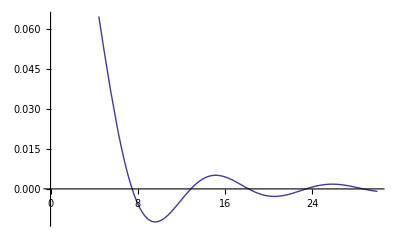

```mathematica
Plot[Re[T00sOrders⟦1⟧ ] /.{N-> 3, a-> 0.6},{z,0,30}]
```

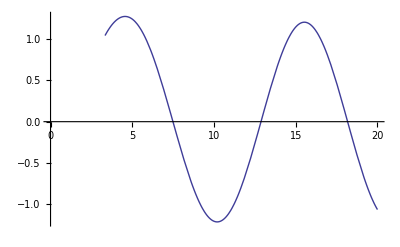

```mathematica
Plot[test44[Z],{Z,0,20}]
```

```mathematica
Monitor[Table[
Assuming[N>3,Integrate[T00sOrders⟦order⟧ z^(N-1),{z,0,Z}]],{order,1, Length@T00s}],order]
```

```mathematica
erg[Z_,A_,n_]:=NIntegrate[Re@Evaluate[T00sOrders⟦1⟧ z^(N-1) /. {N-> n,a->A}],{z,0,Z}]
```

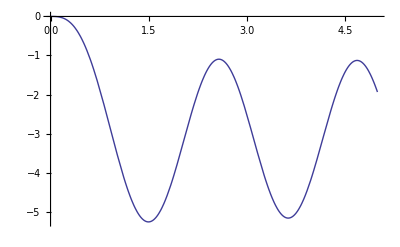

```mathematica
Plot[erg[z,3,3],{z,0,5}]
```

#### Zeichnen von g00 durch Interpolation

```mathematica
(*Manipulate[
Function[Strip,Plot[Evaluate[Strip[1-2Ms⟦order⟧/z^(N-2)] /. {Z-> z,a-> l,N-> n}] ,{z,0,10},WorkingPrecision->10]
] /@{Re,Im},
{{l,1},0,10},{n,3,7,1}, {order,1, Length@Ms,1}]*)
```

```mathematica
Evaluate[Re[1-2Ms⟦3⟧/z^(N-2)]/. {z-> z,a-> 1, N-> 5}]
```

1-2 Re[1/z^3(1/(4 Z^15)(ⅈ Z^15 Gamma[4,-ⅈ Z]-ⅈ Z^15 Gamma[4,ⅈ Z]-ⅈ Z^11 Gamma[8,-ⅈ Z]+ⅈ Z^11 Gamma[8,ⅈ Z])+1/8 Z^5 ((ⅈ (6 Z^10-Z^10 Gamma[4,-ⅈ Z]+Z^2 Gamma[12,-ⅈ Z]))/Z^15-(ⅈ (6 Z^10-Z^10 Gamma[4,ⅈ Z]+Z^2 Gamma[12,ⅈ Z]))/Z^15)+1/Z^5(6 ⅈ Z^5 Log[-ⅈ Z]+ⅈ Z^5 Gamma[4,-ⅈ Z] Log[-ⅈ Z]-ⅈ Z^5 Gamma[4,ⅈ Z] Log[-ⅈ Z]-6 ⅈ Z^5 Log[ⅈ Z]+ⅈ Z^5 Gamma[4,-ⅈ Z] Log[ⅈ Z]-ⅈ Z^5 Gamma[4,ⅈ Z] Log[ⅈ Z]-ⅈ Z^5 Gamma[4,-ⅈ Z] Log[Z^2]+ⅈ Z^5 Gamma[4,ⅈ Z] Log[Z^2]+ⅈ Z^5 MeijerG[{{},{1,1}},{{0,0,4},{}},-ⅈ Z]-ⅈ Z^5 MeijerG[{{},{1,1}},{{0,0,4},{}},ⅈ Z]))]

```mathematica
Plot[Evaluate[Re[1-2Ms⟦3⟧/z^(N-2)]/. {z-> z,a-> 1, N-> 3}],{z,0,1},WorkingPrecision->10]
```

-Graphics-